```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/SLattice/math"];
```

```mathematica
(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)//Simplify
```

(m^2 x^4)/(96 π^2)

```mathematica
(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)/.{x->15,m->10^-5}//N
```

5.34311×10^-9

```mathematica
Sqrt[4 53+2]//N
```

14.6287

```mathematica
dNdata=Import["chaotic_dN.dat"]//Flatten;
Ndata1=Import["Ncl_lattice_RK4_1.dat"]//Flatten;
Ndata2=Import["Ncl_lattice_RK4_2.dat"]//Flatten;
Ndata3=Import["Ncl_lattice_RK4_3.dat"]//Flatten;
Ndata4=Import["Ncl_lattice_RK4_4.dat"]//Flatten;
Ndata5=Import["Ncl_lattice_RK4_5.dat"]//Flatten;
Ndata6=Import["Ncl_lattice_RK4_6.dat"]//Flatten;
```

```mathematica
L=17;
```

```mathematica
dNmap=Flatten[Table[{x,y,z,dNdata[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];dNmap1=Flatten[Table[{x,y,z,Ndata1[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata1]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
dNmap2=Flatten[Table[{x,y,z,Ndata2[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata2]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
dNmap3=Flatten[Table[{x,y,z,Ndata3[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata3]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
dNmap4=Flatten[Table[{x,y,z,Ndata4[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata4]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
dNmap5=Flatten[Table[{x,y,z,Ndata5[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata5]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
dNmap6=Flatten[Table[{x,y,z,Ndata6[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata6]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
```

```mathematica
ListDensityPlot3D[dNmap]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[dNmap1]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[dNmap2]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[dNmap3]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[dNmap4]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[dNmap5]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[dNmap6]
```

-Graphics3D-

```mathematica
dNk[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap[[i,1]];yy=dNmap[[i,2]];zz=dNmap[[i,3]];
dNmap[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap]}];
dNk1[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap1[[i,1]];yy=dNmap1[[i,2]];zz=dNmap1[[i,3]];
dNmap1[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap1]}];
dNk2[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap2[[i,1]];yy=dNmap2[[i,2]];zz=dNmap2[[i,3]];
dNmap2[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap2]}];
dNk3[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap3[[i,1]];yy=dNmap3[[i,2]];zz=dNmap3[[i,3]];
dNmap3[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap3]}];
dNk4[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap4[[i,1]];yy=dNmap4[[i,2]];zz=dNmap4[[i,3]];
dNmap4[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap4]}];
dNk5[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap5[[i,1]];yy=dNmap5[[i,2]];zz=dNmap5[[i,3]];
dNmap5[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap5]}];
dNk6[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap6[[i,1]];yy=dNmap6[[i,2]];zz=dNmap6[[i,3]];
dNmap6[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap6]}];
```

```mathematica
kmax=L-1;
c=0.1;
```

```mathematica
Variance[dNdata]
Variance[Ndata1]
Variance[Ndata2]
Variance[Ndata3]
Variance[Ndata4]
Variance[Ndata5]
Variance[Ndata6]
```

1.33038×10^-8

8.74566×10^-9

6.82809×10^-9

5.71016×10^-9

9.40803×10^-9

6.74368×10^-9

6.58527×10^-9

```mathematica
ParallelSum[Abs[dNk[kx,ky,kz]]^2/L^3,{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}]//AbsoluteTiming
ParallelSum[Abs[dNk1[kx,ky,kz]]^2/L^3,{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}]//AbsoluteTiming
ParallelSum[Abs[dNk2[kx,ky,kz]]^2/L^3,{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}]//AbsoluteTiming
ParallelSum[Abs[dNk3[kx,ky,kz]]^2/L^3,{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}]//AbsoluteTiming
ParallelSum[Abs[dNk4[kx,ky,kz]]^2/L^3,{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}]//AbsoluteTiming
ParallelSum[Abs[dNk5[kx,ky,kz]]^2/L^3,{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}]//AbsoluteTiming
ParallelSum[Abs[dNk6[kx,ky,kz]]^2/L^3,{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}]//AbsoluteTiming
```

{12.3227,1.33011×10^-8}

{12.4973,8.74388×10^-9}

{12.0988,6.8267×10^-9}

{12.1713,5.70899×10^-9}

{12.1356,9.40611×10^-9}

{12.1547,6.74231×10^-9}

{12.0583,6.58393×10^-9}

```mathematica
Pkdata[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
Pkdata1[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk1[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
Pkdata2[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk2[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
Pkdata3[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk3[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
Pkdata4[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk4[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
Pkdata5[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk5[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
Pkdata6[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk6[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
```

```mathematica
PkList=Select[ParallelTable[Pkdatas=Pkdata[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkList1=Select[ParallelTable[Pkdatas=Pkdata1[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkList2=Select[ParallelTable[Pkdatas=Pkdata2[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkList3=Select[ParallelTable[Pkdatas=Pkdata3[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkList4=Select[ParallelTable[Pkdatas=Pkdata4[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkList5=Select[ParallelTable[Pkdatas=Pkdata5[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkList6=Select[ParallelTable[Pkdatas=Pkdata6[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
```

{19.7103,Null}

{19.3632,Null}

{19.3704,Null}

{19.4092,Null}

{19.3647,Null}

{19.4421,Null}

{19.3599,Null}

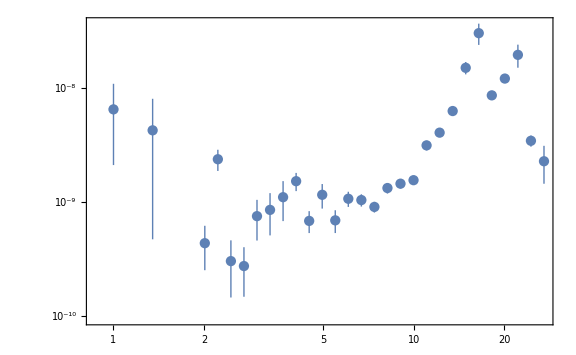

```mathematica
ListLogLogPlot[PkList,GridLines->{None,{(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)/.{x->15,m->10^-5}}},Joined->False]
```

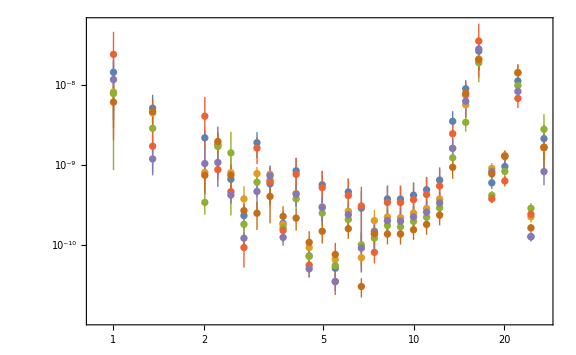

```mathematica
ListLogLogPlot[{PkList1,PkList2,PkList3,PkList4,PkList5,PkList6},GridLines->{None,{(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)/.{x->15,m->10^-5}}},Joined->False]
```

```mathematica
PkListWOe=Select[ParallelTable[Pkdatas=Pkdata[E^lnk];If[Length[Pkdatas]>1,Total[Pkdatas]/(c L^3),None],{lnk,0,Log[Sqrt[3]kmax],c}],Positive];//AbsoluteTiming
```

{29.0663,Null}

```mathematica
c Total[PkListWOe]
Variance[dNdata]
```

1.29302×10^-8

1.33038×10^-8